### Visualizing and solving a 2 variable LP

#### First let’s plot a feasible region using the RegionPlot command:

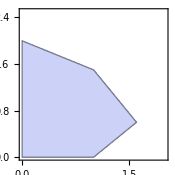

```mathematica
a=RegionPlot[{3x1+2x2≤6  && 
		       x1-    x2≤1  &&
		       x1+ 2x2≤4 &&
                          x1≥0 &&  x2≥0},{x1,0,2},{x2,0,2.5}]
```

#### Now we’ll add in some objective contours with labels. We’ll combine the plots of both using the “Show” command;

```mathematica
b=Plot[{1-x1,1.5-x1,2-x1},{x1,0,2.5},PlotStyle->{{Black,Dashed}}];
```

This next bit of code handles text labels for the contour lines.  The pair of numbers at the end specifies the coordinate location of the label.

```mathematica
c=Text["z=1",{1.1,.02}];  
d=Text["z=1.5",{1.55,.1}];
e = Text["z=2",{1.8,.3}];
```

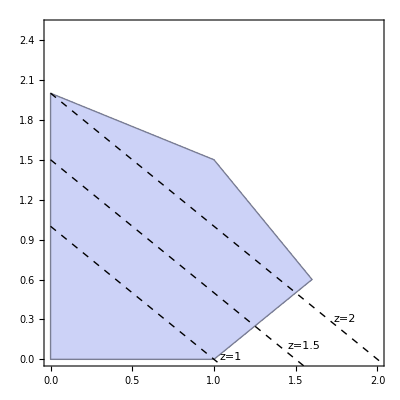

```mathematica
Show[a,b,Graphics[{c,d,e}]]
```

#### Next we can demonstrate the sliding of the contour line parallel to itself until it leaves the feasible region by dragging the slider. The last point it touches is the optimal solution.

```mathematica
Manipulate[Show[a,Plot[{z-x1},{x1,0,2.5} ]],{z,0,3}]
```

#### Let’s look at the same feasible region but this time in 3-space by using the Plot3D and RegionFunction commands:

The first entry is for the function of the surface we want to plot (z = f(x,y) function).  We’ll start with the function z = 0.  RegionFunction then restricts the plot of the surface based on the constraints within it.

```mathematica
Plot3D[0,{x1,0,2},{x2,0,3},
RegionFunction->Function[{x1,x2},
3x1+2x2≤6&&
x1-    x2≤1  &&
x1+ 2x2≤4 &&
x1≥0 &&  x2≥0],BoxStyle->Directive[Dashed]]
```

-Graphics3D-

#### Now add in a linear objective function (z = x1 + x2):

```mathematica
d=Plot3D[{x1+x2,0},{x1,0,2},{x2,0,3},
RegionFunction->Function[{x1,x2},
3x1+2x2≤6&&
x1-    x2≤1  &&
x1+ 2x2≤4 &&
x1≥0 &&  x2≥0],BoxStyle->Directive[Dashed]]
```

-Graphics3D-

#### Solve it (there are several ways to do so in Mathematica: Maximize, NMaximize, LinearProgramming, etc.):

```mathematica
Maximize[x1+x2,3x1+2x2≤6&&
x1-    x2≤1  &&
x1+ 2x2≤4 &&
x1≥0 &&  x2≥0,{x1,x2}]
```

{5/2,{x1→1,x2→3/2}}

#### Plot the solution along with its projection on the x1 : x2 plane.

```mathematica
e=ListPointPlot3D[{{1,3/2,5/2},{1,3/2,0}},PlotStyle->{AbsolutePointSize[8]}];
```

```mathematica
Show[d,e]
```

-Graphics3D-

#### Add a slider to see how things change when objective coefficients change:

```mathematica
Manipulate[Plot3D[{t*t1*x1+t*t2*x2,0},{x1,0,2},{x2,0,3},
RegionFunction->Function[{x1,x2},
3x1+2x2≤6&&
x1-    x2≤1  &&
x1+ 2x2≤4 &&
x1≥0 &&  x2≥0],BoxStyle->Directive[Dashed],PlotRange->{{0,2},{0,3},{0,24}}],{t,0,3},{t1,1,3},{t2,1,3}]
```

### Visualizing and solving a 3 variable LP

#### Now let’s turn it into a 3D problem (by adding an additional variable, x3, into the objective and constraints). First we’ll plot the feasible region, which is now 3-dimensional, using the RegionPlot3D command:

```mathematica
a1=RegionPlot3D[3 x1 +2x2 +x3≤ 6 &&
                         x1-x2+x3≤1&& 
                         x1+2x2+1x3≤4&&
                           x1≥0&&x2≥0&&x3≥0,
{x1,0,3},{x2,0,3},{x3,0,3},
Mesh->All,PlotPoints->100,AxesLabel->Automatic]
```

-Graphics3D-

Rotate it around to get a feel for the polyhedral shape.  For 3-variable problems, constraints are represented as planes dividing 3-space into two parts.

#### We can also visualize the objective contours as planes. Using the objective z = x1 + x2 + x3, we can plot the countours z = 1.5, z = 2.5 (solving each equation for x3 and plotting the surface):

```mathematica
a2=Plot3D[{1.5-x1-x2,2.5-x1-x2} ,{x1,0,3},{x2,0,3},AxesLabel->Automatic];
Show[a1,a2]
```

-Graphics3D-

#### Let’s introduce a slider again to allow us to alter the value of one of the objective contours and watch it slide paralellel to itself.

```mathematica
Manipulate[Show[a1,Plot3D[{1.5-x1-x2,z-x1-x2} ,{x1,0,3},{x2,0,3},AxesLabel->Automatic]],{z,1,5}]
```

#### Now let’s solve it.

```mathematica
Maximize[x1+x2+x3,3x1+2x2+x3≤6&&
x1-    x2+x3≤1  &&
x1+ 2x2+x3≤4 &&
x1≥0 &&  x2≥0 && x3≥0,{x1,x2,x3}]
```

{3,{x1→1,x2→1,x3→1}}

#### Plotting it again with a dot at the optimal solution Mathematica found, but another at the point (0,1,2) because by inspection, this is optimal as well (z=3) though Mathematica did not report it - we’ll refine our methods to catch this situation soon.

```mathematica
e=ListPointPlot3D[{{1,1,1},{0,1,2}},PlotStyle->{AbsolutePointSize[8]}];
```

```mathematica
Manipulate[Show[a1,e,Plot3D[{1.5-x1-x2,z-x1-x2} ,{x1,0,3},{x2,0,3},AxesLabel->Automatic]],{z,1,5}]
```